Working Directory: C:\Users\Prajwal\Dropbox\nEDM\psi-nedm\Analysis

(ASCII) Rawdata Directory: C:\Users\Prajwal\Dropbox\nEDM\rawdata

Runs in the list: 11369

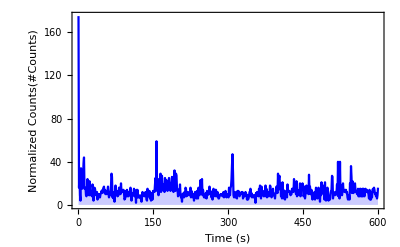

Number of Cycles: 696.

```mathematica
OS="win";(*or linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
If[OS=="win",
Print["Working Directory: ",curDir=SetDirectory["C:\\Users\\Prajwal\\Dropbox\\nEDM\\psi-nedm\\Analysis"]];
Print["(ASCII) Rawdata Directory: ",AscDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\rawdata"];
];
If[OS=="linux",
Print["Working Directory:",curDir=SetDirectory["/home/prajwal/Dropbox/nEDM/psi-nedm/Analysis"]];
Print["(faster) Rawdata Directory:",fastDir="/home/prajwal/nEDM/rawdata"];
Print["(ASCII) Rawdata Directory:",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];
];
Print["Runs in the list: ",runNum=11369];
metaStructure={Real,Word,Real,Real,Real,Real,Real};
metaStructure2={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
metadata=ReadList[StringJoin[AscDir,"/",IntegerString[runNum,10,6],"/",IntegerString[runNum,10,6],"_Meta3.edm"],metaStructure2];
EDAListPlot[metadata[[1;;600,32]],PlotStyle->{Blue,Red,Gray},Joined->True,Filling->Axis,PlotRange->Full,Frame->True,PlotRange->Full,FrameLabel->{"Time (s)","Normalized Counts(#Counts)"},TicksStyle->Directive[FontSize->40],LabelStyle->{18},ImageSize->{1000}]
Print["Number of Cycles: ",maxCy=metadata[[-1]][[2]]];
```

```mathematica
DateObject[metadata[[1]][[1]]]
```

Mon 22 Aug 2016 16:47:50GMT-4.

```mathematica
Clear[data,histdata2]
data={};
(*histbeg2=96.112226;histlast2=96.112233;*)
(*runi=157*)
For[runi=200,runi<400(*Dimensions[runNum][[1]]*),runi++,
data=Join[data,ReadList[StringJoin[AscDir,"\\",IntegerString[runNum,10,6],"\\",IntegerString[runNum,10,6],"_UCNdet_",IntegerString[runi,10,3],"_0001.fast.ascii"],metaStructure]];
];
dimdata=Dimensions[data][[1]]
(*histdata=HistogramList[Select[data[[1;;dimdata,{3,7}]],#[[1]]==ChNum&][[;;,2]],{100,3000,binw}];*)
Dimensions[data]
```

42871

{42871,7}

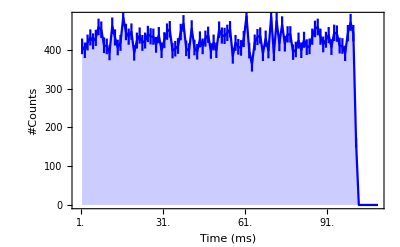

```mathematica
histbeg2=1;histlast2=110;binw2=1;
ptdat2=Table[{0,{0,0}},{k,1,Round[(histlast2-histbeg2)/binw2]}];
histdata2=HistogramList[data[[Round[1];;dimdata,4]]/1000000000,{histbeg2,histlast2,binw2}];
For[i=1,i<=Dimensions[histdata2[[2]]][[1]],i++,
ptdat2[[i]][[1]]=(histdata2[[1]][[i]]+((-histdata2[[1]][[1]]+histdata2[[1]][[2]])/2));
ptdat2[[i]][[2]][[1]]+=histdata2[[2]][[i]];
ptdat2[[i]][[2]][[2]]=Sqrt[ptdat2[[i]][[2]][[1]]];
];
tks=Table[SetPrecision[k,3],{k,histbeg2,histlast2,10binw2}];
EDAListPlot[ptdat2,PlotStyle->{Blue,Red,Gray},Joined->True,Filling->Axis,PlotRange->Full,Frame->True,PlotRange->Full,FrameLabel->{"Time (ms)","#Counts"},TicksStyle->Directive[FontSize->40],FrameTicks->{{Automatic,None},{tks,None}},LabelStyle->{18},ImageSize->{1000}]
```

```mathematica
subset=Select[Select[data[[1;;dimdata,{3,4,5,6,7}]],#[[2]]>=96112220000&],#[[2]]<=96112240000&];
(*subset[[;;,3]]=13.6*subset[[;;,3]];
subset[[;;,4]]=13.6*subset[[;;,4]];*)
subset[[;;,2]]=SetPrecision[subset[[;;,2]]/1000000000,11];
TableForm[subset]
Dimensions[subset][[1]]
```

8. | 96.11222843 | 387.441 | 542.36 | 642.429
18. | 96.112228544 | 490.137 | 544.329 | 753.148
15. | 96.11222861 | 774.883 | 820.76 | 1240.66
13. | 96.112228636 | 308.086 | 359.944 | 508.079
14. | 96.112228728 | 629.009 | 673.354 | 912.588
8. | 96.11222882 | 452.793 | 510.851 | 644.763
11. | 96.112228824 | 546.152 | 604.283 | 897.563
12. | 96.112228832 | 479.634 | 518.072 | 765.985
6. | 96.112228838 | 388.608 | 437.33 | 558.406
17. | 96.11222884 | 590.498 | 626.383 | 776.633
18. | 96.112228984 | 561.323 | 620.183 | 899.022
15. | 96.112229026 | 676.855 | 725.067 | 1097.12
19. | 96.112229036 | 333.76 | 376.793 | 572.701
7. | 96.112229096 | 306.919 | 345.357 | 456.732
14. | 96.112229128 | 616.172 | 655.85 | 874.077
8. | 96.11222921 | 394.443 | 438.497 | 621.423
4. | 96.112229264 | 359.434 | 411.292 | 561.761
12. | 96.112229284 | 462.129 | 495.899 | 671.458
11. | 96.112229286 | 560.156 | 621.788 | 713.178
6. | 96.112229286 | 501.807 | 544.694 | 804.641
5. | 96.112229348 | 511.143 | 553.519 | 742.353
13. | 96.112229352 | 263.74 | 310.93 | 392.547
18. | 96.11222937 | 641.846 | 691.37 | 872.181
15. | 96.11222943 | 776.05 | 811.424 | 1057.44
17. | 96.11222944 | 380.439 | 441.998 | 588.748
16. | 96.112229506 | 364.102 | 409.833 | 495.826
14. | 96.112229532 | 521.646 | 564.824 | 741.04
11. | 96.112229742 | 368.77 | 408.228 | 525.292
18. | 96.112229804 | 368.77 | 421.795 | 620.11
15. | 96.112229876 | 351.265 | 405.311 | 511.288
6. | 96.112230158 | 225.229 | 266.949 | 280.662
18. | 96.11223028 | 287.08 | 330.769 | 408.885

32

```mathematica
cnt=Table[0,{k,1,dimdata}];j=1;
For[i=2,i≤dimdata,i++,
If[(data[[i]][[4]]-data[[i-1]][[4]]<10000),
cnt[[j]]=i;
j++;
];
];
Print["# of burst events: ",Dimensions[DeleteCases[cnt,0]][[1]]];
cleandata=Select[data[[1;;dimdata,{3,4,6,5,7}]],(#[[3]]-#[[4]])>150&];
Print["# of clean events: ",Dimensions[cleandata][[1]]];
Print["# of all events: ",Dimensions[data][[1]]];
Print["# Difference: ",Dimensions[data][[1]]-Dimensions[cleandata][[1]]];
Mean[data[[;;,6]]-data[[;;,5]]]
Max[data[[;;,6]]-data[[;;,5]]]
Min[data[[;;,6]]-data[[;;,5]]]
StandardDeviation[data[[;;,6]]-data[[;;,5]]]
Mean[subset[[;;,4]]-subset[[;;,3]]]
Max[subset[[;;,4]]-subset[[;;,3]]]
Min[subset[[;;,4]]-subset[[;;,3]]]
StandardDeviation[subset[[;;,4]]-subset[[;;,3]]]
```

# of burst events: 5713

# of clean events: 38614

# of all events: 42871

# Difference: 4257

340.802

3030.68

32.53

204.763

50.3037

154.919

33.77

20.5746

```mathematica
data[[Position[data,9.6112228838*^10][[1]][[1]]+1]]
```

{220873.,QDC_X3,17.,9.61122×10^10,590.498,626.383,776.633}

```mathematica
N[data[[28]][[4]]-data[[27]][[4]]]<10000
```

False

```mathematica
0.00001*10^9
```

10000.

```mathematica
aaa={1,2,3};bbb={2,3,4};
ccc=Join[ccc,bbb]
```

{1,2,3,2,3,4,2,3,4,2,3,4,2,3,4,2,3,4,2,3,4,2,3,4,2,3,4}